```mathematica
wbar=Integrate[ 1/Sqrt[2π VG]Exp[-(p-Ep)^2/2/VG-(p-o)^2/2/VS],{p,-Infinity,Infinity},Assumptions->{VG>0,VS>0}]
```

ⅇ^(-(Ep-o)^2/(2 (VG+VS))) √(VS/(VG+VS))

```mathematica
wAA=Integrate[ 1/Sqrt[2π VGprime]Exp[-(p-Epprime - 2a)^2/2/VGprime-(p-o)^2/2/VS],{p,-Infinity,Infinity},Assumptions->{VGprime>0,VS>0}]
```

ⅇ^(-(2 a+Epprime-o)^2/(2 (VGprime+VS))) √(VS/(VGprime+VS))

```mathematica
wAA/.{}
```

ⅇ^(-(2 a+Epprime-o)^2/(2 (VG+VS))) √(VS/(VG+VS))

```mathematica
wAa=Integrate[ 1/Sqrt[2π VGprime]Exp[-(p-Epprime - a)^2/2/VGprime-(p-o)^2/2/VS],{p,-Infinity,Infinity},Assumptions->{VGprime>0,VS>0}]
```

ⅇ^(-(a+Epprime-o)^2/(2 (VGprime+VS))) √(VS/(VGprime+VS))

```mathematica
waa=Integrate[ 1/Sqrt[2π VGprime]Exp[-(p-Epprime)^2/2/VGprime-(p-o)^2/2/VS],{p,-Infinity,Infinity},Assumptions->{VGprime>0,VS>0}]
```

ⅇ^(-(Epprime-o)^2/(2 (VGprime+VS))) √(VS/(VGprime+VS))

```mathematica
wAA/wbar
```

ⅇ^((Ep-o)^2/(2 (VG+VS))-(2 a+Epprime-o)^2/(2 (VG+VS)))

```mathematica
1+(Ep-o)^2/(2 (VG+VS))-1+(2a+Epprime-o)^2/(2 (VG+VS))/.{o->0,Ep->0}
```

(2 a+Epprime)^2/(2 (VG+VS))

```mathematica
wA=p wAA + (1-p)wAa//Simplify
wa=p wAa + (1-p)waa//Simplify
```

(-ⅇ^(-(a+Epprime-o)^2/(2 (VGprime+VS))) (-1+p)+ⅇ^(-(2 a+Epprime-o)^2/(2 (VGprime+VS))) p) √(VS/(VGprime+VS))

(-ⅇ^(-(Epprime-o)^2/(2 (VGprime+VS))) (-1+p)+ⅇ^(-(a+Epprime-o)^2/(2 (VGprime+VS))) p) √(VS/(VGprime+VS))

```mathematica
p(1-p)(wA-wa)/wbar//Simplify
```

ⅇ^((Ep-o)^2/(2 (VG+VS))) (1-p) p (ⅇ^(-(a+Epprime-o)^2/(2 (VG+VS))) (1-2 p)+ⅇ^(-(Epprime-o)^2/(2 (VG+VS))) (-1+p)+ⅇ^(-(2 a+Epprime-o)^2/(2 (VG+VS))) p)

```mathematica
ⅇ^((Ep-o)^2/(2 (VG+VS))) (1-p) p ((1-(a+Epprime-o)^2/(2 (VG+VS)) )(1-2 p)+(1-(Epprime-o)^2/(2 (VG+VS))) (-1+p)+(1-(2 a+Epprime-o)^2/(2 (VG+VS))) p)//Simplify
```

(a ⅇ^((Ep-o)^2/(2 (VG+VS))) (-1+p) p (a+2 Epprime-2 o+2 a p))/(2 (VG+VS))

```mathematica
wAA=Integrate[ 1/Sqrt[2π VG]Exp[-(p-Epprime - 2a)^2/2/VG-(p-o)^2/2/VS],{p,-Infinity,Infinity},Assumptions->{VG>0,VS>0}];
wAa=Integrate[ 1/Sqrt[2π VG]Exp[-(p-Epprime - a)^2/2/VG-(p-o)^2/2/VS],{p,-Infinity,Infinity},Assumptions->{VG>0,VS>0}];
waa=Integrate[ 1/Sqrt[2π VG]Exp[-(p-Epprime)^2/2/VG-(p-o)^2/2/VS],{p,-Infinity,Infinity},Assumptions->{VG>0,VS>0}];
wA=p wAA + (1-p)wAa//Simplify
wa=p wAa + (1-p)waa//Simplify
```

(-ⅇ^(-(a+Epprime-o)^2/(2 (VG+VS))) (-1+p)+ⅇ^(-(2 a+Epprime-o)^2/(2 (VG+VS))) p) √(VS/(VG+VS))

(-ⅇ^(-(Epprime-o)^2/(2 (VG+VS))) (-1+p)+ⅇ^(-(a+Epprime-o)^2/(2 (VG+VS))) p) √(VS/(VG+VS))

```mathematica
dp=p(1-p)(wA-wa)/wbar//Simplify
```

ⅇ^((Ep-o)^2/(2 (VG+VS))) (1-p) p (ⅇ^(-(a+Epprime-o)^2/(2 (VG+VS))) (1-2 p)+ⅇ^(-(Epprime-o)^2/(2 (VG+VS))) (-1+p)+ⅇ^(-(2 a+Epprime-o)^2/(2 (VG+VS))) p)

```mathematica
%/.{Ep->0,o->0}//Simplify
```

(1-p) p (ⅇ^(-(a+Epprime)^2/(2 (VG+VS))) (1-2 p)+ⅇ^(-Epprime^2/(2 (VG+VS))) (-1+p)+ⅇ^(-(2 a+Epprime)^2/(2 (VG+VS))) p)

```mathematica
Simplify[(1-2p)(1-(a^2-2a(Epprime-o))/(2(VG+VS)))-(1-p)+p(1-4(a^2-a(Epprime-o))/(2(VG+VS)))]
%*ⅇ^((Ep-o)^2/(2 (VG+VS))) (1-p) p//Simplify
```

-(a (a-2 Epprime+2 o+2 a p))/(2 (VG+VS))

(a ⅇ^((Ep-o)^2/(2 (VG+VS))) (-1+p) p (a-2 Epprime+2 o+2 a p))/(2 (VG+VS))

```mathematica
Solve[VG==4Ne u Ea2/(1+Ne Ea2/(VS+VG)),VG]/.{VS->1,u->0.025,Ne->10000,Ea2->0.01}
```

{{VG→-91.1098},{VG→0.109758}}

```mathematica
2 * 10000 * 25
```

500000

```mathematica
stuff=DSolve[{
0==-γ x(1-x)D[f[x],x]+x(1-x)/2D[f[x],{x,2}],
f[0]==θ,
f[1]==0},
f[x],
{x,0,1}]
```

{{f[x]→((ⅇ^(2 γ)-ⅇ^(2 x γ)) θ)/(-1+ⅇ^(2 γ))}}

```mathematica
n=20;
i=10;
NIntegrate[Binomial[n,i]x^(i-1)(1-x)^(n-i-1)f[x]/.stuff/.{γ->1,θ->1},{x,0,1}]
```

{0.144164}

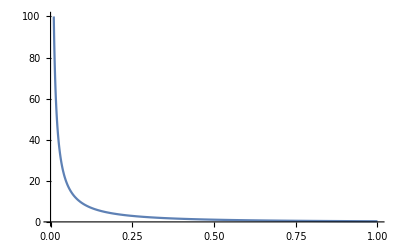

```mathematica
Plot[f[x]/x/(1-x)/.stuff/.{γ->-1,θ->1},{x,0,1},PlotRange->{0,100}]
```

```mathematica
stuff=NDSolve[{
0==-γ x(1-x)(1-2x)D[g[x],x]+x(1-x)/2D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{θ->1,γ->1},
g[x],
{x,0,1}]
```

{{g[x]→InterpolatingFunction[…][x]}}

```mathematica
n=20;
i=10;
NIntegrate[Binomial[n,i]x^(i-1)(1-x)^(n-i-1)g[x]/.stuff,{x,0,1}]
```

{0.100004}

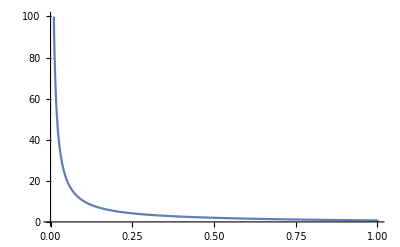

```mathematica
Plot[g[x]/x/(1-x)/.stuff,{x,0,1},PlotRange->{0,100}]
```

Below showing that stabilizing selection results in underdominance

```mathematica
wbar=1/Sqrt[2π VG]Integrate[Exp[-x^2/(2 VG)]Exp[-x^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
w11=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a)^2/(2 VG)]Exp[-(x+2a)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
w01=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a)^2/(2 VG)]Exp[-(x+a)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
w00=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a)^2/(2 VG)]Exp[-(x)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
```

(√((VG VS)/(VG+VS)))/(√VG)

(ⅇ^(-(2 a^2 (-1+p)^2)/(VG+VS)) √((VG VS)/(VG+VS)))/(√VG)

(ⅇ^(-(a^2 (1-2 p)^2)/(2 (VG+VS))) √((VG VS)/(VG+VS)))/(√VG)

(ⅇ^(-(2 a^2 p^2)/(VG+VS)) √((VG VS)/(VG+VS)))/(√VG)

```mathematica
Simplify[wbar]
```

(√((VG VS)/(VG+VS)))/(√VG)

```mathematica
w11=Normal[Series[w11,{a,0,2}]]
w01=Normal[Series[w01,{a,0,2}]]
w00=Normal[Series[w00,{a,0,2}]]
```

(√((VG VS)/(VG+VS)))/(√VG)-(2 a^2 (-1+p)^2 √((VG VS)/(VG+VS)))/(√VG (VG+VS))

(√((VG VS)/(VG+VS)))/(√VG)-(a^2 (1-2 p)^2 √((VG VS)/(VG+VS)))/(2 √VG (VG+VS))

(√((VG VS)/(VG+VS)))/(√VG)-(2 a^2 p^2 √((VG VS)/(VG+VS)))/(√VG (VG+VS))

```mathematica
w1dot=p w11+(1-p)w01//Simplify
w0dot=p w01+(1-p)w00//Simplify
```

(((VG VS)/(VG+VS))^(3/2) (a^2 (-1+p)+2 (VG+VS)))/(2 VG^(3/2) VS)

(((VG VS)/(VG+VS))^(3/2) (-a^2 p+2 (VG+VS)))/(2 VG^(3/2) VS)

```mathematica
(w1dot-w0dot)/wbar//Simplify
```

(a^2 (-1+2 p))/(2 (VG+VS))

Two locus model:

```mathematica
w1111=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a+2q b)^2/(2 VG)]Exp[-(x+2a+2b)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
w0111=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a+2q b)^2/(2 VG)]Exp[-(x+a+2b)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
w0011=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a+2q b)^2/(2 VG)]Exp[-(x+2b)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
w1101=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a+2q b)^2/(2 VG)]Exp[-(x+2a+b)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
w0101=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a+2q b)^2/(2 VG)]Exp[-(x+a+b)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
w0001=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a+2q b)^2/(2 VG)]Exp[-(x+b)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
w1100=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a+2q b)^2/(2 VG)]Exp[-(x+2a)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
w0100=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a+2q b)^2/(2 VG)]Exp[-(x+a)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
w0000=1/Sqrt[2π VG]Integrate[Exp[-(x+2p a+2q b)^2/(2 VG)]Exp[-(x)^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
```

(ⅇ^(-(2 (a (-1+p)+b (-1+q))^2)/(VG+VS)) √((VG VS)/(VG+VS)))/(√VG)

(ⅇ^(-(a (-1+2 p)+2 b (-1+q))^2/(2 (VG+VS))) √((VG VS)/(VG+VS)))/(√VG)

(ⅇ^(-(2 (a p+b (-1+q))^2)/(VG+VS)) √((VG VS)/(VG+VS)))/(√VG)

(ⅇ^(-(2 a (-1+p)+b (-1+2 q))^2/(2 (VG+VS))) √((VG VS)/(VG+VS)))/(√VG)

(ⅇ^(-(a+b-2 a p-2 b q)^2/(2 (VG+VS))) √((VG VS)/(VG+VS)))/(√VG)

(ⅇ^(-(2 a p+b (-1+2 q))^2/(2 (VG+VS))) √((VG VS)/(VG+VS)))/(√VG)

(ⅇ^(-(2 (a (-1+p)+b q)^2)/(VG+VS)) √((VG VS)/(VG+VS)))/(√VG)

(ⅇ^(-(a (-1+2 p)+2 b q)^2/(2 (VG+VS))) √((VG VS)/(VG+VS)))/(√VG)

(ⅇ^(-(2 (a p+b q)^2)/(VG+VS)) √((VG VS)/(VG+VS)))/(√VG)

```mathematica
w1111=Normal[Series[
Replace[Replace[w1111,a->a t,All],b->b t,All]
,{t,0,2}]]/.{t->1}//Simplify
w1101=Normal[Series[
Replace[Replace[w1101,a->a t,All],b->b t,All]
,{t,0,2}]]/.{t->1}//Simplify
w0111=Normal[Series[
Replace[Replace[w0111,a->a t,All],b->b t,All]
,{t,0,2}]]/.{t->1}//Simplify
w0101=Normal[Series[
Replace[Replace[w0101,a->a t,All],b->b t,All]
,{t,0,2}]]/.{t->1}//Simplify
w1100=Normal[Series[
Replace[Replace[w1100,a->a t,All],b->b t,All]
,{t,0,2}]]/.{t->1}//Simplify
w0100=Normal[Series[
Replace[Replace[w0100,a->a t,All],b->b t,All]
,{t,0,2}]]/.{t->1}//Simplify
w0011=Normal[Series[
Replace[Replace[w0011,a->a t,All],b->b t,All]
,{t,0,2}]]/.{t->1}//Simplify
w0001=Normal[Series[
Replace[Replace[w0001,a->a t,All],b->b t,All]
,{t,0,2}]]/.{t->1}//Simplify
w0000=Normal[Series[
Replace[Replace[w0000,a->a t,All],b->b t,All]
,{t,0,2}]]/.{t->1}//Simplify
```

(√((VG VS)/(VG+VS)) (1-(2 (a (-1+p)+b (-1+q))^2)/(VG+VS)))/(√VG)

(√((VG VS)/(VG+VS)) (2-(2 a (-1+p)+b (-1+2 q))^2/(VG+VS)))/(2 √VG)

(√((VG VS)/(VG+VS)) (2-(a (-1+2 p)+2 b (-1+q))^2/(VG+VS)))/(2 √VG)

(√((VG VS)/(VG+VS)) (2-(a+b-2 a p-2 b q)^2/(VG+VS)))/(2 √VG)

(((VG VS)/(VG+VS))^(3/2) (-2 a^2 (-1+p)^2-4 a b (-1+p) q-2 b^2 q^2+VG+VS))/(VG^(3/2) VS)

(√((VG VS)/(VG+VS)) (2-(a (-1+2 p)+2 b q)^2/(VG+VS)))/(2 √VG)

(((VG VS)/(VG+VS))^(3/2) (-2 a^2 p^2-4 a b p (-1+q)-2 b^2 (-1+q)^2+VG+VS))/(VG^(3/2) VS)

(√((VG VS)/(VG+VS)) (2-(2 a p+b (-1+2 q))^2/(VG+VS)))/(2 √VG)

(((VG VS)/(VG+VS))^(3/2) (-2 a^2 p^2-4 a b p q-2 b^2 q^2+VG+VS))/(VG^(3/2) VS)

```mathematica
wbar=1/Sqrt[2π VG]Integrate[Exp[-x^2/(2 VG)]Exp[-x^2/(2VS)],{x,-Infinity,Infinity},Assumptions->VG>0∧VG∈Reals∧VS>0∧VS∈Reals]
```

(√((VG VS)/(VG+VS)))/(√VG)

```mathematica
wAB=p q w1111+p(1-q)w1101+(1-p)q w0111+(1-p)(1-q)w0101//Simplify
wAb=p q w1101+p(1-q)w1100+(1-p)q w0101+(1-p)(1-q)w0100//Simplify
waB=p q w0111+p(1-q)w0101+(1-p)q w0011+(1-p)(1-q)w0001//Simplify
wab=p q w0101+p(1-q)w0100+(1-p)q w0001+(1-p)(1-q)w0000//Simplify
```

(((VG VS)/(VG+VS))^(3/2) (a^2 (-1+p)+b^2 (-1+q)-2 a b (-1+p) (-1+q)+2 (VG+VS)))/(2 VG^(3/2) VS)

(((VG VS)/(VG+VS))^(3/2) (a^2 (-1+p)-b^2 q-2 a b (-1+p) q+2 (VG+VS)))/(2 VG^(3/2) VS)

(((VG VS)/(VG+VS))^(3/2) (-a^2 p+b^2 (-1+q)-2 a b p (-1+q)+2 (VG+VS)))/(2 VG^(3/2) VS)

(((VG VS)/(VG+VS))^(3/2) (-a^2 p-b^2 q-2 a b p q+2 (VG+VS)))/(2 VG^(3/2) VS)

```mathematica
wAB/wbar-1//Simplify
wAb/wbar-1//Simplify
waB/wbar-1//Simplify
wab/wbar-1//Simplify
```

(a^2 (-1+p)+b^2 (-1+q)-2 a b (-1+p) (-1+q))/(2 (VG+VS))

(a^2 (-1+p)-b^2 q-2 a b (-1+p) q)/(2 (VG+VS))

(-a^2 p+b^2 (-1+q)-2 a b p (-1+q))/(2 (VG+VS))

-(a^2 p+b^2 q+2 a b p q)/(2 (VG+VS))

Expected mean fitness, assuming normal distribution with mean zero and variance VS/2Ne for the mean phenotype of a population.
We could also plug in the SHOC model for expected VG, depending on Ne, VS, and mu.

```mathematica
f[pbar_]:=1/Sqrt[2 π (VS/2/Ne)]Exp[-pbar^2/(2 VS/2/Ne)];
g[p_]:=1/Sqrt[2 π VG]Exp[-(p-pbar)^2/(2 VG)];
h[p_]:=Integrate[f[pbar]*g[p],{pbar,-Infinity,Infinity},Assumptions->{VG>0,VS>0,Ne>0}]
```

```mathematica
Integrate[f[pbar],{pbar,-Infinity,Infinity},Assumptions->{VG>0,VS>0,Ne>0}]
Integrate[g[p],{p,-Infinity,Infinity},Assumptions->{VG>0,VS>0,Ne>0}]
Integrate[h[p],{p,-Infinity,Infinity},Assumptions->{VG>0,VS>0,Ne>0}]
```

1

1

1

```mathematica
h[p]
```

(ⅇ^(-(Ne p^2)/(2 Ne VG+VS)))/(√π √(2 VG+VS/Ne))

```mathematica
w[p_]:=Exp[-p^2/(2VS)];
Ef=Integrate[w[p]h[p],{p,-Infinity,Infinity},Assumptions->{VG>0,VS>0,Ne>0}]
```

√2 √((Ne VS)/(VS+2 Ne (VG+VS)))

```mathematica
Simplify[%]
```

√2 √((Ne VS)/(VS+2 Ne (VG+VS)))

```mathematica
Limit[Ef,Ne->Infinity]/.{VS->1}//Simplify
```

√(1/(1+VG))

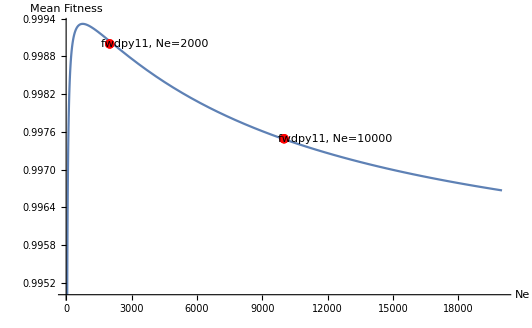

```mathematica
p1=Plot[Ef/.{VG->4*U*VS/(1+VS/Ne/SD^2)}/.{VS->1,SD->0.01,U->0.0025},{Ne,50,20000},PlotRange->All,AxesLabel->{"Ne","Mean Fitness"}];
p2=ListPlot[{{2000,0.999}},PlotStyle->Red,PlotLabels->Placed[{"fwdpy11, Ne=2000"},Right]];
p3=ListPlot[{{10000,0.997492}},PlotStyle->Red,PlotLabels->Placed[{"fwdpy11, Ne=10000"},Right]];
Show[p1, p2,p3]
```

```mathematica
0.002
0.1^2/8
```

0.002

0.00125

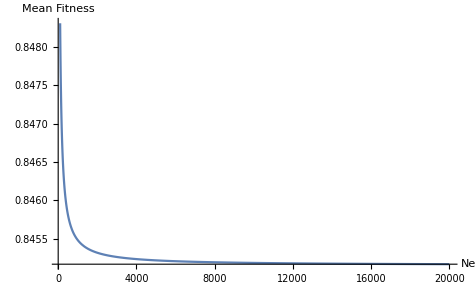

```mathematica
Plot[Ef/.{VG->4*U*VS/(1+VS/Ne/VM)}/.{VS->1,VM->0.25,U->0.1},{Ne,100,20000},PlotRange->All,AxesLabel->{"Ne","Mean Fitness"}]
```

```mathematica
Solve[D[Ef/.{VG->4*U*VS/(1+VS/Ne/VM)}/.{VS->1},Ne]==0,Ne]//Simplify
```

{{Ne→(1-(2 √2 √U)/(√VM))/(8 U-VM)},{Ne→(1+(2 √2 √U)/(√VM))/(8 U-VM)}}

```mathematica
Solve[D[Ef/.{VG->4*U*VS/(1+VS/Ne/VM)},Ne]==0,Ne]//Simplify
```

{{Ne→-(VS-(2 √2 √U VS^(3/2))/(√VM))/(VM-8 U VS)},{Ne→-(VS+(2 √2 √U VS^(3/2))/(√VM))/(VM-8 U VS)}}

```mathematica
D[Ef/.{VG->4*U*VS/(1+VS/Ne/VM)},Ne]//Simplify
```

(2 Ne VM VS+VS^2+Ne^2 VM (VM-8 U VS))/(√2 √((Ne (Ne VM+VS))/(2 Ne^2 (VM+4 U VM)+VS+Ne (VM+2 VS))) (2 Ne^2 (VM+4 U VM)+VS+Ne (VM+2 VS))^2)

```mathematica
(-SD^2-2 √2 SD √U)/(SD^4-8 SD^2 U)/.{SD->0.1,U->0.0013}
```

5049.51

```mathematica
U > SD^2/8/ VS
```

U>SD^2/(8 VS)

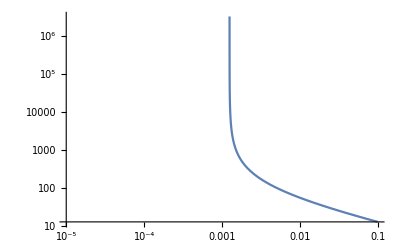

```mathematica
LogLogPlot[(-SD^2-2 √2 SD √U)/(SD^4-8 SD^2 U)/.{SD->0.1},{U,0.001,0.1},PlotRange->{{0.00001,0.1},All}]
```

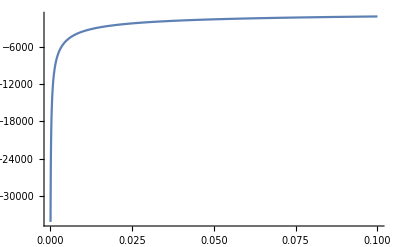

```mathematica
Plot[(-SD^2+2 √2 SD √U)/(SD^4-8 SD^2 U)/.{SD->0.001},{U,0.0001,0.1},PlotRange->{{0.0001,0.1},All}]
```

```mathematica
Simplify[(-SD^2-2 √2 SD √U)/(SD^4-8 SD^2 U)]
```

-(SD+2 √2 √U)/(SD^3-8 SD U)

```mathematica
Solve[SD^3-8 SD U==0,U]
```

{{U→SD^2/8}}

```mathematica
Ef/.{VG->4*U*VS/(1+VS/Ne/SD^2)}//Simplify
```

√2 √((Ne VS)/(VS+2 Ne (VS+(4 Ne SD^2 U VS)/(Ne SD^2+VS))))